# Plotting frog populations

## Ericka Florio July 22 2022

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/eflorio/Documents/Coding/fun/frogs

### Importing the data

```mathematica
lam0p5=Import["frogs05.dat","Data"];
lam0p7=Import["frogs07.dat","Data"];
lam0p9=Import["frogs09.dat","Data"];
```

```mathematica
lam1=Import["frogs1.dat","Data"];
lam2=Import["frogs2.dat","Data"];
lam3=Import["frogs3.dat","Data"];
```

```mathematica
lam3p4=Import["frogs34.dat","Data"];
lam4=Import["frogs4.dat","Data"];
```

### Plots for Ni=0.4

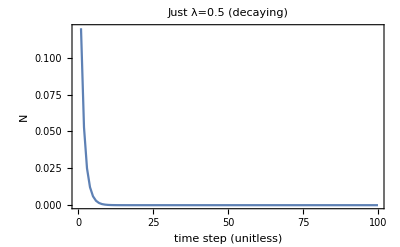

```mathematica
ListPlot[lam0p5[[;;,1]],Joined->True,PlotRange->All,GridLines->None,Frame->True,FrameLabel->{"time step (unitless)","N"},PlotLabel->"Just λ=0.5 (decaying)"]
```

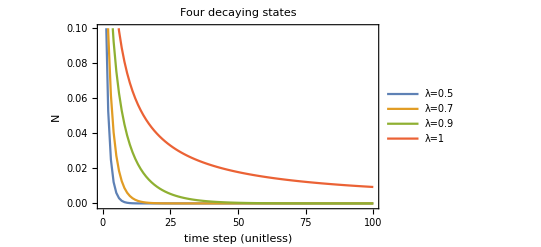

```mathematica
ListPlot[{lam0p5[[;;,1]],lam0p7[[;;,1]],lam0p9[[;;,1]],lam1[[;;,1]]},Joined->True,PlotRange->{All,{-0.001,0.1}},GridLines->None,Frame->True,FrameLabel->{"time step (unitless)","N"},PlotLabel->"Four decaying states",PlotLegends->{"λ=0.5","λ=0.7","λ=0.9","λ=1"}]
```

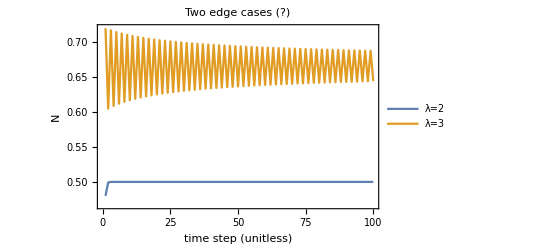

```mathematica
ListPlot[{lam2[[;;,1]],lam3[[;;,1]]},Joined->True,PlotRange->All,GridLines->None,Frame->True,FrameLabel->{"time step (unitless)","N"},PlotLabel->"Two edge cases (?)",PlotLegends->{"λ=2","λ=3"}]
```

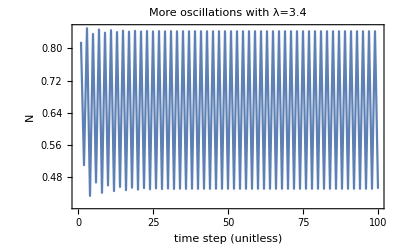

```mathematica
ListPlot[lam3p4[[;;,1]],PlotRange->All,Joined->True,Frame->True,GridLines->None,FrameLabel->{"time step (unitless)","N"},PlotLabel->"More oscillations with λ=3.4" ]
```

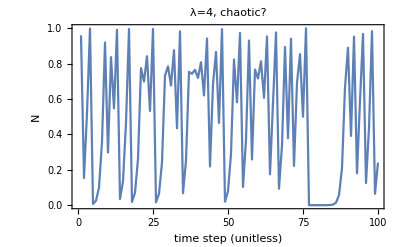

```mathematica
ListPlot[lam4[[;;,1]],PlotRange->All,Joined->True,Frame->True,GridLines->None,FrameLabel->{"time step (unitless)","N"},PlotLabel->"λ=4, chaotic?"]
```

```mathematica
(*cool :)*)
```